## Classes 7

Лабораторная работа №7.

### Элементарная описательная статистика

```mathematica
data= RandomInteger[50,20] (*Создадим набор данных (20 случайных чисел от 0 до 50) и сохраним его под именем data*)
```

{10,10,50,17,46,50,9,22,6,40,6,3,31,23,13,1,20,18,27,38}

```mathematica
Mean[data] (*нахождение среднего значения для data:*)
```

22

```mathematica
Median[data] (*Найдем медиану*)
```

19

```mathematica
Max[data] (*найдем максимальное число*)
```

50

```mathematica
Variance[data] // N (*Находим дисперсию.Ищем среднее арифметическое,вычитаем из каждого это число,потом делаем сумму квадратов из полученного,и делим на list.count-1*)
```

248.842

```mathematica
StandardDeviation[data] // N (*среднеквадратическое отклонение*)
```

15.7747

```mathematica
Quantile[data,1/2] (*Находит квантиль (значение, которое заданная случайная величина не превышает с фиксированной вероятностью)
Первый агрумент - набор данных, второй - число q в диапазоне от 0 до 1*)
```

18

```mathematica
Quartiles[data]  // N (*Находит (1/4, 1/2 and 3/4)квантили для списка*)
```

{9.5,19.,34.5}

### Работа со статистическим распределением

```mathematica
(*PDF дает плотность вероятности для распределения, оцененного в точке x*)
```

```mathematica
PDF[NormalDistribution[μ,σ],x] 
PDF[NormalDistribution[1,3],3]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

1/(3 ⅇ^(2/9) √(2 π))

```mathematica
(*Здесь функция плотности показана на графике при заданных x значениях μ и  σ
```

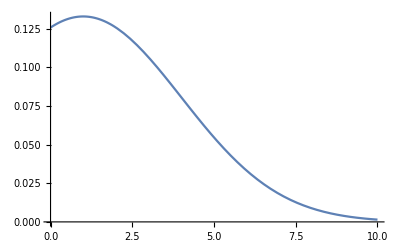

```mathematica
Plot[PDF[NormalDistribution[1,3],x],{x,0,10}]
```

```mathematica
(* среднее значение для 40 попыток при биномаильном распределении с вероятностью выигрыша .7
```

```mathematica
Mean[BinomialDistribution[40,.7]]
```

28.

```mathematica
(*дает характеристическую функцию для распределения в зависимости от переменной t.
получаем общую формулу характеристической функции
```

```mathematica
CharacteristicFunction[NormalDistribution[μ,σ],t] 
CharacteristicFunction[CauchyDistribution[μ,σ],t]  (*распределени коши*)
```

ⅇ^(ⅈ t μ-(t^2 σ^2)/2)

ⅇ^(ⅈ t μ-t σ Sign[t])

```mathematica
(*дает n-й момент для случайной переменной Х в Пуассоновом рапределении*)
```

```mathematica
Moment[PoissonDistribution[μ],n]
Moment[PoissonDistribution[μ],3]
Moment[CauchyDistribution[μ,σ],n]
```

```mathematica
(* BellB - число Белла или многочлен.
```

Piecewise[{{BellB[n,μ], n≥0}, {0, True}}]

μ+3 μ^2+μ^3

Piecewise[{{1, n==0}, {Indeterminate, True}}]

```mathematica
(*
Использование функции RandomVariate дает возможность генерировать случайные числа из распределений
Геометрическое распределение описывает количество попыток до неудачи, где существует вероятность успеха p для каждой попытки. 
Сгенерируем 20 чисел из геометрического распределения с параметром вероятности успеха p=1/3
```

```mathematica
RandomVariate[PoissonDistribution[15],10]
RandomVariate[GeometricDistribution[1/3],20]
```

{16,13,15,18,11,13,11,15,17,14}

{0,0,1,1,0,1,4,3,1,0,0,0,5,0,0,2,1,1,1,1}

```mathematica
(* 
Сгенерируем 1000 чисел из гамма-распределения, и сохраним их под именем data:
Далее, применим функцию Histogram для построения гистограммы этих значений по шкале плотности вероятности:
```

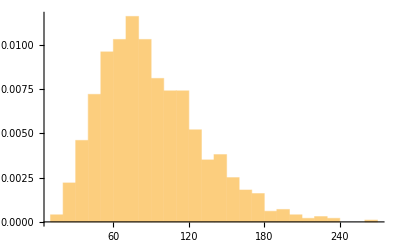

```mathematica
data=RandomVariate[GammaDistribution[5,18],1000];
hist=Histogram[data,Automatic,"ProbabilityDensity"]
```

```mathematica
(*Для визуализации функции теоретической плотности, воспользуемся функцией Plot
```

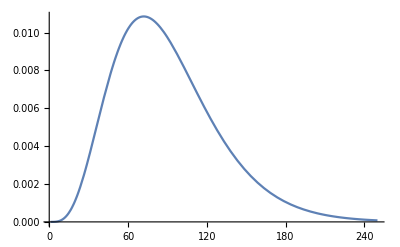

```mathematica
pl=Plot[PDF[GammaDistribution[5,18],x],{x,1,250}]
```

```mathematica
(* применим команду Show для отображения двух графиков вместе
```

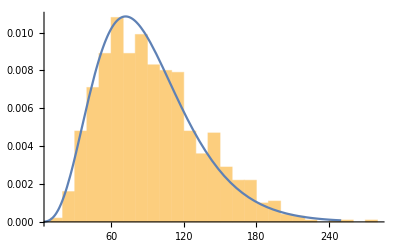

```mathematica
Show[hist,pl]
```

```mathematica
(* найдем прогноз максимального правдоподобия параметров (оценку), используя функцию FindDistributionParameters
```

```mathematica
alphabeta=FindDistributionParameters[data,GammaDistribution[α,β]]
```

{α→5.10682,β→18.3839}

```mathematica
(* При помощи функции EstimatedDistribution, результаты могут быть сгруппированы в объект, представляющий собой распределение
```

```mathematica
gdist=EstimatedDistribution[data,GammaDistribution[α,β]]
```

GammaDistribution[5.10682,18.3839]

```mathematica
(* вычисляем также и логарифмическое правдоподобие, применив функцию LogLikelihood к оцениваемому распределению:
```

```mathematica
LogLikelihood[gdist,gdata]
```

LogLikelihood[GammaDistribution[5.10682,18.3839],gdata]

```mathematica
(* Создание контурного графика с помощью функции ContourPlot в окрестности найденных значений обеспечивает качественное сравнение.
Точки на определенной линии имеют одинаковое правдоподобие
```

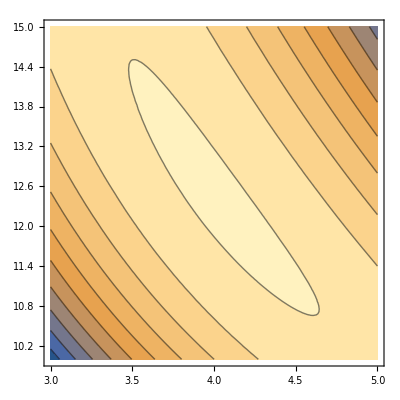

```mathematica
data = RandomVariate[GammaDistribution[4, 12.5], 10^3];
ContourPlot[LogLikelihood[GammaDistribution[α,β],data],{α,3,5},{β,10,15}]
```

## Проверка гипотез о математическом ожидании

```mathematica
(*сгенерируем примерный набор данных
```

```mathematica
data = RandomVariate[NormalDistribution[17,4], 10]
```

{11.2437,18.48,10.5727,18.6428,16.9558,22.4448,17.4733,15.0895,13.5831,20.6118}

```mathematica
(*возвращает значение теста при нулевой гипотезе, что математическое ожидание равно 17
```

```mathematica
TTest[data, 17]
```

0.698461

```mathematica
(* проверим, будет ли разница между двумя математическими ожиданиями существенно отличаться от предполагаемого значения.
В этом случае, нулевой гипотезой является предположение, что математические ожидания равны (разность равна 0):
```

```mathematica
data2 = RandomVariate[NormalDistribution[9,1],10];
TTest[{data,data2}]
```

0.000119917

```mathematica
(* математическое ожидание для data является в 4 раза больше чем для data2
```

```mathematica
TTest[{data, data2},4]
```

0.0235074

```mathematica
(*проверяет, равно ли среднее значение data- data2 нулю.*)
```

```mathematica
PairedTTest[{data,data2}]
```

0.000359985

## Работа со столбцами данных

```mathematica
(* Создадим некоторый набор данных для дальнейшей обработки
```

```mathematica
data = RandomInteger[{2, 20},{3,5}]
```

{{17,18,2,11,13},{12,12,8,6,16},{13,9,9,8,4}}

```mathematica
MatrixForm[data] (*MatrixForm группирует списки внутри другого списка и печатает матрицу*)
```

(17 | 18 | 2 | 11 | 13
12 | 12 | 8 | 6 | 16
13 | 9 | 9 | 8 | 4)

```mathematica
(* Функция Grid отображает данные таким же самым образом, но без скобок
```

```mathematica
Grid[data]
```

17 | 18 | 2 | 11 | 13
12 | 12 | 8 | 6 | 16
13 | 9 | 9 | 8 | 4

```mathematica
Mean[data](*среднее арифметическое каждого столбца*)
StandardDeviation[data] (*дает среднеквадратичное отклонение элементов каждого столбца*)
Median[data]
```

{14,13,19/3,25/3,11}

{√7,√21,√(43/3),√(19/3),√39}

{13,12,8,8,13}

```mathematica
(* Для вычислений выбираем отдельный столбец(второй столбец из набора данных data)
```

```mathematica
col =data[[All, 2]](*получаем колонку*)
Mean[col] (*среднее арифметическое столбца*)
StandardDeviation[col] (*дает среднеквадратичное отклонение элементов столбца*)
```

{18,12,9}

13

√21

```mathematica
(* линейный график для столбцов как для отдельных наборов данных
```

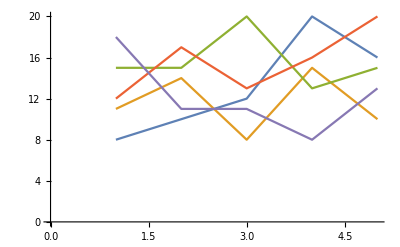

```mathematica
ListLinePlot[data]
```

```mathematica
(* Построим график для столбцов, транспонировав данные (строки меняются со столбцами) )
```

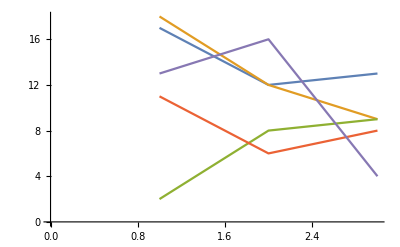

```mathematica
ListLinePlot[Transpose[data]]
```

```mathematica
(* применим функцию Normalize к каждому элементу транспонирванных данных( используя команду Map )
Normalize gives the normalized form of a vector v
```

```mathematica
Map[Normalize,Transpose[data]]
```

{{17/(√602),6 √(2/301),13/(√602)},{6/(√61),4/(√61),3/(√61)},{2/(√149),8/(√149),9/(√149)},{11/(√221),6/(√221),8/(√221)},{13/21,16/21,4/21}}

```mathematica
(* Транспонируем результат выше
```

```mathematica
Transpose[%]
```

{{17/(√602),6/(√61),2/(√149),11/(√221),13/21},{6 √(2/301),4/(√61),8/(√149),6/(√221),16/21},{13/(√602),3/(√61),9/(√149),8/(√221),4/21}}

```mathematica
(* транспонируем найденный ранее набор данных и найдем максимальный жлемент каждой строки
```

```mathematica
Map[Max,Transpose[data]]
Map[Max,data]
```

{17,18,9,11,16}

{18,16,13}

## Выполнение операций с подгруппами данных

```mathematica
(* Следующие данные представляют урожайность для трех типов грунта и двух сортов семян кукурузы
```

```mathematica
agdata={{clay,seedB,175},{silty,seedB,180},{clay,seedB,165},{sandy,seedA,168},{clay,seedA,184},{sandy,seedB,171},{sandy,seedB,173},{sandy,seedA,189},{clay,seedA,186},{silty,seedB,174},{clay,seedA,192},{clay,seedA,184},{clay,seedA,179},{sandy,seedA,182},{sandy,seedB,177},{silty,seedA,180},{clay,seedB,175},{silty,seedB,181},{sandy,seedA,176},{silty,seedB,190}};
```

```mathematica
(* группировка в подсписки по первому элементу каждой точки данных
```

```mathematica
bySoilType=GatherBy[agdata,First]
```

{{{clay,seedB,175},{clay,seedB,165},{clay,seedA,184},{clay,seedA,186},{clay,seedA,192},{clay,seedA,184},{clay,seedA,179},{clay,seedB,175}},{{silty,seedB,180},{silty,seedB,174},{silty,seedA,180},{silty,seedB,181},{silty,seedB,190}},{{sandy,seedA,168},{sandy,seedB,171},{sandy,seedB,173},{sandy,seedA,189},{sandy,seedA,182},{sandy,seedB,177},{sandy,seedA,176}}}

```mathematica
(* применяем Table для вывода типа грунта и средней урожайности для каждой группы
 (извлечение каждого типа из каждого подсписка и вычисления среднего Mean значения последнего элемента в списке)
```

```mathematica
Table[{x[[1,1]],N[Mean[x[[All,-1]]]]},{x,bySoilType}]
```

{{clay,180.},{silty,181.},{sandy,176.571}}

```mathematica
(* сгруппируем  данные по второму элементу каждой точки данных (используем чистую функцию)
```

```mathematica
bySeedType=GatherBy[agdata,#[[2]] &]
```

{{{clay,seedB,175},{silty,seedB,180},{clay,seedB,165},{sandy,seedB,171},{sandy,seedB,173},{silty,seedB,174},{sandy,seedB,177},{clay,seedB,175},{silty,seedB,181},{silty,seedB,190}},{{sandy,seedA,168},{clay,seedA,184},{sandy,seedA,189},{clay,seedA,186},{clay,seedA,192},{clay,seedA,184},{clay,seedA,179},{sandy,seedA,182},{silty,seedA,180},{sandy,seedA,176}}}

```mathematica
(* Вычисление среднего в разрезе сортов семян
используем только что сформированный набор данных bySeedType. И возьмем второй элемент для получения сорта семян.
```

```mathematica
Table[{x[[1,2]],N[Mean[x[[All,-1]]]]},{x,bySeedType}]
```

{{seedB,176.1},{seedA,182.}}

```mathematica
(*дапазон урожайности и минимальную и максимальную урожайность в зависимости от сорта семян*)
```

```mathematica
Table[{x[[1,2]],{N[Min[x[[All,-1]]]],N[Max[x[[All,-1]]]]}},{x,bySeedType}]
```

{{seedB,{165.,190.}},{seedA,{168.,192.}}}

```mathematica
(* Следующий набор данных содержит информацию от виде лекарства, возрасте пациента и времени выздоровления пациентов, получавших лечение в определенных условиях)
```

```mathematica
meddata={{drugB,67,18},{drugB,48,18},{drugA,33,16},{drugB,76,33},{drugB,33,3},{placebo,40,15},{drugB,78,28},{drugB,54,13},{placebo,46,23},{drugA,36,12},{drugA,69,30},{drugA,78,40},{placebo,77,37},{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24},{placebo,25,9},{drugB,75,25},{drugB,22,3},{placebo,51,25},{placebo,27,8},{placebo,47,20},{placebo,69,34},{drugB,52,16}};
```

```mathematica
(*группируем по виду лекарства*)
```

```mathematica
byDrug=GatherBy[meddata,First] 
(* получения значений размера выборки, среднего, медианы и диапазона для выбранного списка *)
describe[values_]:={Length[values],Mean[values],Median[values],{Min[values],Max[values]}}
```

```mathematica
(*Применим функцию Table вместе с describe для получения статистических результатов в разрезе вида лекарства. 
Последовательность результатов для каждого вида лекарства совпадает с параметрами, указанными в определении функции describe (размер выборки, среднее, медиана, диапазон выборки)*)
```

```mathematica
Table[{x[[1,1]],describe[N[x[[All,-1]]]]},{x,byDrug} ]
```

{{drugB,{9,17.4444,18.,{3.,33.}}},{drugA,{8,24.,21.,{12.,40.}}},{placebo,{8,21.375,21.5,{8.,37.}}}}

```mathematica
(* группировка по возрасту
каждый возраст делится на 10, затем, с помощью функции IntegerPart берутся только те цифры, которые находятся слева от десятичной точки.Далее, функция GatherBy используется для выборки данных в группы в зависимости от полученного числа
```

```mathematica
byAgeGroup=GatherBy[meddata,IntegerPart[#[[2]]/10] &]
```

{{{drugB,67,18},{drugA,69,30},{placebo,69,34}},{{drugB,48,18},{placebo,40,15},{placebo,46,23},{drugA,45,16},{placebo,47,20}},{{drugA,33,16},{drugB,33,3},{drugA,36,12},{drugA,36,18}},{{drugB,76,33},{drugB,78,28},{drugA,78,40},{placebo,77,37},{drugA,79,36},{drugB,75,25}},{{drugB,54,13},{drugA,58,24},{placebo,51,25},{drugB,52,16}},{{placebo,25,9},{drugB,22,3},{placebo,27,8}}}

```mathematica
(*  вычисления статистических данных в разрезе возрастных групп. 
Функция Sort применяется здесь для сортировки данных по увеличению возраста группы
```

```mathematica
Table[{10IntegerPart[x[[1,2]]/10],describe[N[x[[All,-1]]]]},{x,byAgeGroup}]//Sort
```

{{20,{3,6.66667,8.,{3.,9.}}},{30,{4,12.25,14.,{3.,18.}}},{40,{5,18.4,18.,{15.,23.}}},{50,{4,19.5,20.,{13.,25.}}},{60,{3,27.3333,30.,{18.,34.}}},{70,{6,33.1667,34.5,{25.,40.}}}}

```mathematica
(*Выполним группировку данных по виду лекарства и возрастной группе 
путем указания обеих функций - First и IntegerPart в списке аргументов функции GatherBy
```

```mathematica
byDrugAndAgeGroup=GatherBy[meddata, {First[#], IntegerPart[#[[2]]/10]} &]
```

{{{drugB,67,18}},{{drugB,48,18}},{{drugA,33,16},{drugA,36,12},{drugA,36,18}},{{drugB,76,33},{drugB,78,28},{drugB,75,25}},{{drugB,33,3}},{{placebo,40,15},{placebo,46,23},{placebo,47,20}},{{drugB,54,13},{drugB,52,16}},{{drugA,69,30}},{{drugA,78,40},{drugA,79,36}},{{placebo,77,37}},{{drugA,45,16}},{{drugA,58,24}},{{placebo,25,9},{placebo,27,8}},{{drugB,22,3}},{{placebo,51,25}},{{placebo,69,34}}}

```mathematica
(* данные отсортированы по виду лекарства и отображены в виде таблицы, при помощи функции Grid
```

```mathematica
Table[{x[[1,1]],10IntegerPart[x[[1,2]]/10],describe[N[x[[All,-1]]]]},{x,byDrugAndAgeGroup}]//Sort//Grid
```

drugA | 30 | {3,15.3333,16.,{12.,18.}}
drugA | 40 | {1,16.,16.,{16.,16.}}
drugA | 50 | {1,24.,24.,{24.,24.}}
drugA | 60 | {1,30.,30.,{30.,30.}}
drugA | 70 | {2,38.,38.,{36.,40.}}
drugB | 20 | {1,3.,3.,{3.,3.}}
drugB | 30 | {1,3.,3.,{3.,3.}}
drugB | 40 | {1,18.,18.,{18.,18.}}
drugB | 50 | {2,14.5,14.5,{13.,16.}}
drugB | 60 | {1,18.,18.,{18.,18.}}
drugB | 70 | {3,28.6667,28.,{25.,33.}}
placebo | 20 | {2,8.5,8.5,{8.,9.}}
placebo | 40 | {3,19.3333,20.,{15.,23.}}
placebo | 50 | {1,25.,25.,{25.,25.}}
placebo | 60 | {1,34.,34.,{34.,34.}}
placebo | 70 | {1,37.,37.,{37.,37.}}

## Замена или удаление недостающих или недействительных данных

```mathematica
(*Следующий код выдает валовой внутренний продукт (ВВП) для каждой страны, внесенной в перечень функции CountryData.*)
```

```mathematica
gdps=Map[CountryData[#,"GDP"]&,CountryData[All]];
```

```mathematica
(*Так выводятся значения gdps для первых 10 стран в алфавитном порядке:*)
```

```mathematica
Take[gdps,10]
```

{1.98071×10^10 $,Missing[NotAvailable],1.47996×10^10 $,1.45164×10^11 $,6.38×10^8 $,3.15507×10^9 $,6.23069×10^10 $,2.11174×10^8 $,1.41506×10^9 $,3.83067×10^11 $}

```mathematica
(*Максимум нельзя определить по исходным данным:*)
```

```mathematica
Max[gdps]
```

Max::nord2: Comparison of 2.09366×10^13 and -∞ is invalid.

Max[Missing[NotAvailable],2.09366×10^13 $]

```mathematica
(*Количество отсутствующих значений в наборе данных может быть определено путем подсчета выражений с заголовком Missing.*)
```

```mathematica
Count[gdps,_Missing]
```

16

```mathematica
(*По сравнению с общим количеством данных в наборе (оно определено при помощи функции Length), 
 количество отсутствующих значений относительно невелико*)
```

```mathematica
Length[gdps]
```

249

```mathematica
filteredgdps=DeleteCases[gdps,_Missing]; (*удаление всех элементов _Missing*)
```

```mathematica
{Length[filteredgdps],Max[filteredgdps]} (*длина оставшихся данных и максимальное значение*)
```

{233,2.09366×10^13 $}

```mathematica
(* дан набор данных, где первый элемент представляет номер одной из двух групп, а два других элемента являются численными результатами измерений свойств отдельных объектов в этих группах*)
```

```mathematica
data={{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{4,88.6,1.9},{1,62.3,1.8},{1,82.7,"NA"},{1,35.5,1.84}};
```

```mathematica
Grid[data,Dividers->All] (*Отображение данных в табличной форме облегчает задачу поиска "проблемных" данных:*)
```

1 | 71.6 | 0.41
2 | 27.2 | 4.96
2 | 59.3 | 0.18
1 | 46. | 2.72
2 | 42.2 | 1.06
1 | 89.1 | 3.75
4 | 88.6 | 1.9
1 | 62.3 | 1.8
1 | 82.7 | NA
1 | 35.5 | 1.84

```mathematica
(*эта функция идентифицирует такие элементы данных, проверяя соответствие данных на входе заданному шаблону.
 Она возвращает значение True (Истина) если данные на входе не совпадают с шаблоном:
Действительные элементы этого набора данных должны содержать 1 или 2 в качестве первого элемента и числа в качестве второго и третьего элемента
```

```mathematica
baddata[entry_]:=Not[MatchQ[entry,{1|2,_?NumberQ,_?NumberQ}]] 
DeleteCases[data,_?baddata] (* Для удаления недействительных данных можно использовать функцию DeleteCases с выражением _?baddata в качестве шаблона:*)
```

{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,35.5,1.84}}

```mathematica
(* является ли запись набора данных недействительной,  проверка соответствия первого элемента записи значениям 1 или 2
```

```mathematica
badgroup[entry_]:=Not[MatchQ[entry[[1]],1|2]]
(*Для удаления недействительных данных, используем функцию DeleteCases с выражением _?baddata в качестве шаблона:*)
filtereddata=DeleteCases[data,_?badgroup]
```

{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,NA},{1,35.5,1.84}}

```mathematica
group1=Select[filtereddata,#[[1]]===1&] (*Используем функцию Select для выборки элементов данных где 1ый элемент ==1*)
```

{{1,71.6,0.41},{1,46.,2.72},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,NA},{1,35.5,1.84}}

```mathematica
group1mean=Mean[Select[group1[[All,3]],NumberQ]] (*Используем функцию Select вновь, для выборки чисел из последнего элемента каждой записи (третьего столбца) списка данных group1, и рассчитаем их среднее значение:*)
```

2.104

```mathematica
filtereddata[[All,3]]=filtereddata[[All,3]]/."NA"->group1mean (*Теперь воспользуемся правилом подстановки для замены NA найденным средним значением*)
```

{0.41,4.96,0.18,2.72,1.06,3.75,1.8,2.104,1.84}

```mathematica
Grid[filtereddata,Dividers->All] (*Применим функцию Grid для отображения отфильтрованных данных*)
```

1 | 71.6 | 0.41
2 | 27.2 | 4.96
2 | 59.3 | 0.18
1 | 46. | 2.72
2 | 42.2 | 1.06
1 | 89.1 | 3.75
1 | 62.3 | 1.8
1 | 82.7 | NA
1 | 35.5 | 1.84

```mathematica
(* функция для выполнения замены всех недействительных записей в определенном столбце на значения,рассчитанные на основе действительных данных,содержащихся в этом столбце.
Эта функция может быть использована для обработки каждого столбца в наборе данных.

аргументы:имя набора данных,номер подлежащего обработке столбца,номер столбца для группировки и функцию,используемую для обработки элементов столбца.
Она группирует по заданному столбцу и заменяет любое нечисленное значение в обрабатываемом столбце результатом указанной функции
```

```mathematica
replaceByGroup[data_,col_,groupcol_,f_]:=Block[{columnvals,funvals,grouped,groups,rules},columnvals=data[[All,{groupcol,col}]];
If[VectorQ[columnvals[[All,2]],NumericQ],
columnvals[[All,2]],
grouped=GatherBy[columnvals,First];
groups=grouped[[All,1,1]];
funvals=Table[f[Select[grouped[[i]][[All,2]],NumericQ]],{i,Length[groups]}];
rules=Table[Rule[{groups[[i]],_?(Not[NumericQ[#]]&)},{groups[[i]],funvals[[i]]}],{i,Length[groups]}];
Replace[columnvals,rules,{1}][[All,2]]]]
(* Для начала,зададим исходные данные заново,опустив запись с группой 4 *)
newdata=DeleteCases[data,_?badgroup]
```

{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,NA},{1,35.5,1.84}}

```mathematica
(* Заменим нечисленные значения данных в 3-ем столбце средним от соответствующей группы *)
```

```mathematica
replaceByGroup[newdata,3,1,Mean]
```

{0.41,4.96,0.18,2.72,1.06,3.75,1.8,2.104,1.84}

```mathematica
(* заменим нечисленные значения в 3-ем столбце медианами от соответствующей группы:
```

```mathematica
replaceByGroup[newdata,3,1,Median]
```

{0.41,4.96,0.18,2.72,1.06,3.75,1.8,1.84,1.84}

```mathematica
(* Применим комбинацию функций Transpose и Grid для отображения "очищенного" набора данных в табличной форме.
В этом примере,в качестве значения для подстановки используется среднее для группы:
```

```mathematica
Grid[Transpose[Table[If[j==1,newdata[[All,j]],replaceByGroup[newdata,j,1,Mean]],{j,Length[newdata[[1]]]}]],Dividers->All]
```

1 | 71.6 | 0.41
2 | 27.2 | 4.96
2 | 59.3 | 0.18
1 | 46. | 2.72
2 | 42.2 | 1.06
1 | 89.1 | 3.75
1 | 62.3 | 1.8
1 | 82.7 | 2.104
1 | 35.5 | 1.84

## Выполнение линейной регрессии

```mathematica
(* Сформируем набор данных:
```

```mathematica
data = Table[{3 + i + RandomReal[{-5, 5}], i + RandomReal[{-5, 5}]}, {i, 1, 10}];
model=LinearModelFit[data,x,x]
(*Воспользуемся функцией LinearModelFit для создания линейной модели для заданного набора данных:*)
```

FittedModel[-3.65848+1.20404 x]

```mathematica
model["BestFit"] (*Извлечем функциональную форму модели:*)
```

-1.92095+0.731447 x

```mathematica
(* Построим график функциональной формы модели:
```

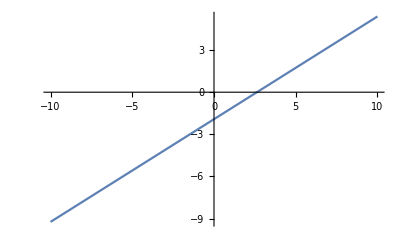

```mathematica
Plot[model["BestFit"], {x, -10, 10}]
```

```mathematica
(*Отобразим данные и линию наилучшего соответствия:*)
```

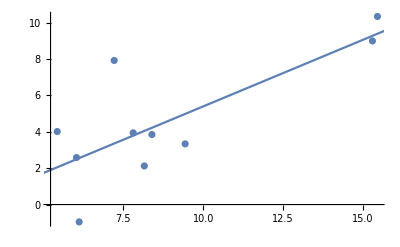

```mathematica
Show[ListPlot[data], Plot[model["BestFit"], {x, 0, 20}]]
```

```mathematica
(*Получим информацию по оценке параметров выполненной регрессии:*)
```

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.92095 | 2.08544 | -0.921126 | 0.383921
x | 0.731447 | 0.217978 | 3.3556 | 0.00999681

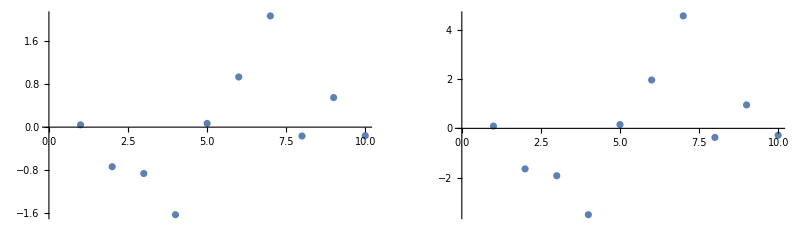

```mathematica
{sr,fr}=model[{"StandardizedResiduals", "FitResiduals"}]; (*Извлечем и отобразим на графике нормализованные и наблюдаемые остатки:*)
{{ListPlot[sr], ListPlot[fr]}}//GraphicsGrid
```

```mathematica
(*Построим график расстояний Кука:*)
```

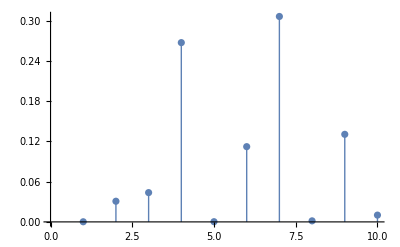

```mathematica
ListPlot[model["CookDistances"], Filling->Axis, FillingStyle->Thick, PlotStyle->Thick]
```

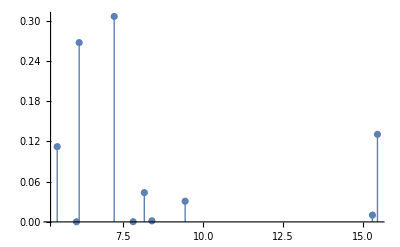

```mathematica
ListPlot[Transpose[{data[[All, 1]], model["CookDistances"]}], Filling->Axis, FillingStyle->Thick, PlotStyle->Thick] (*Как вариант, построим график расстояний Кука в зависимости от предикторного значения:*)
```

```mathematica
(*все возможные использования model
В предыдущих примерах были показаны лишь несколько свойств, поддерживаемых функцией LinearModelFit
```

```mathematica
model["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}